```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
data = Delete[Import["E:\Google Drive\Advanced_Lab\Cell2.csv","csv"],{1}]
```

{{1.952,0.135,0.014},{1.905,0.131,0.009},{1.887,0.161,0.004},{1.892,0.151,0.006},{1.905,0.161,0.004},{1.922,0.155,0.007},{1.941,0.138,0.002},{2.157,0.146,0.002},{2.212,0.131,0.009},{2.999,0.118,0.013},{3.669,0.135,0.004},{4.426,0.086,0.009},{5.529,0.1,0.005},{5.94,0.118,0.004},{7.055,0.124,0.002},{9.843,0.077,0.009}}

```mathematica
{m1,m2,m3,m4}=Graphics/@{Circle[{0,0},1],Disk[{0,0},1],Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}],Polygon[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5}}]};
```

```mathematica
data[[All,1;;2]]
```

{{1.952,0.135},{1.905,0.131},{1.887,0.161},{1.892,0.151},{1.905,0.161},{1.922,0.155},{1.941,0.138},{2.157,0.146},{2.212,0.131},{2.999,0.118},{3.669,0.135},{4.426,0.086},{5.529,0.1},{5.94,0.118},{7.055,0.124},{9.843,0.077}}

```mathematica
dataplot = ErrorListPlot[data, ImageSize -> Large, Frame -> True, FrameLabel -> {"Air Mass","ln[V]"},PlotRange-> {{0,11},{0.05,.18}}, PlotStyle -> Black, GridLines-> Automatic, GridLinesStyle->Directive[Gray,Dashed]];
```

```mathematica
fit = NonlinearModelFit[data[[All,1;;2]], a x +b, {a,b},x, Weights -> data[[All,3]]^-2]
```

FittedModel[0.155884-0.00551262 x]

```mathematica
V[X_] = Exp[0.15588358726626203-0.005512620805061086 X]
```

ⅇ^(0.155884-0.00551262 X)

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | -0.00551262 | 0.00125899 | -4.37861 | 0.000630253
b | 0.155884 | 0.0053907 | 28.9171 | 6.92673×10^-14

```mathematica
Δa = 0.0012589901730714716; Δb = 0.005390701833076339;
```

```mathematica
model = Plot[Normal[fit],{x,0,15},PlotStyle -> {Black,Thick} ];
```

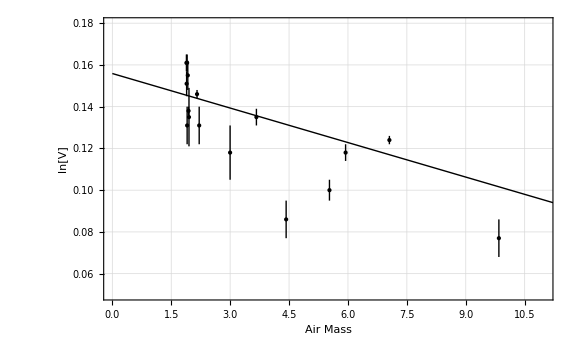

```mathematica
Show[dataplot, model]
```

Optical Depth at one airmass

τ_1= (0.0081±0.0017)
ln(I_o) = (0.1586±0.0073)

```mathematica
f = 1 - V[1]/V[0]
```

0.00549745

```mathematica
V[1]/V[0]
```

0.994503

```mathematica
f = 1 - ⅇ^-τ
```

0.00549745

```mathematica
df = √(D[f,τ]^2 Δa^2)
```

General::ivar: 0.00551262 is not a valid variable.

0.00125899 √((∂_0.00551262 0.00549745)^2)

```mathematica
τ = 0.005512620805061086
```

0.00551262

```mathematica
df
```

0.00125899 √((∂_0.00551262 0.00549745)^2)

```mathematica
f
```

0.00549745

```mathematica
ⅇ^-τ
```

0.994503